```mathematica
hbar = 1.0546*^-34;
bmagn = 9.2740*^-24;
B0 = 0.35;
g1 = {2.0030, 2.0026, 2.0023};
g2 = {2.0062, 2.0051, 2.0022};
g2 = {2, 2, 2};
gFrame = {-10, -128, -83}*Pi/180;
eeFrame = {0,  90, 0}*Pi/180;
dipolar = -4.7642;
JJ = 0.028;
```

```mathematica
erot[ang_] := Transpose[{{Cos[ang[[3]]], Sin[ang[[3]]], 0}, {-Sin[ang[[3]]], Cos[ang[[3]]], 0}, {0, 0, 1}}.{{Cos[ang[[2]]], 0, -Sin[ang[[2]]]}, {0, 1, 0}, {Sin[ang[[2]]], 0, Cos[ang[[2]]]}}.{{Cos[ang[[1]]], Sin[ang[[1]]], 0}, {-Sin[ang[[1]]], Cos[ang[[1]]], 0}, {0, 0, 1}}];
rVers[θ_, ϕ_] := {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]};
ErotG[g_, gFrame_] := erot[gFrame].g.Transpose[erot[gFrame]];
EffG[g_, gFrame_, θ_, ϕ_] := Sqrt[Dot[#^2 & /@ rVers[θ, ϕ], #^2 & /@ ErotG[g, gFrame]]];
dd[dipolar_, θ_] := dipolar*(Cos[θ]^2 - 1/3);
xi[dipolar_, J_, B0_,  θ_, ϕ_] := ArcTan[bmagn*B0/hbar*(EffG[g1, gFrame, θ, ϕ] - EffG[g2, {0, 0, 0}, θ, ϕ]), (2*J + dd[dipolar, θ])*1*^6];
```

```mathematica
cβ0[θ_, ϕ_, τ_] := Sin[2*(JJ - dd[dipolar, θ])*τ]*Sin[2xi[dipolar, JJ, B0, θ, ϕ]]^2;
cβ[τ_] := NIntegrate[Sin[θ]*cβ0[θ, ϕ, τ], {θ, 0, Pi}, {ϕ, 0, 2Pi}, Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}]
c2β0[θ_, ϕ_, τ_] := Sin[2*(JJ - dd[dipolar, θ])*τ]*Cos[xi[dipolar, JJ, B0, θ, ϕ]]^4;
c2β[τ_] := NIntegrate[Sin[θ]*c2β0[θ, ϕ, τ], {θ, 0, Pi}, {ϕ, 0, 2Pi}, Method->{"GlobalAdaptive","MaxErrorIncreases"->10000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {θ,ϕ} = {1.55661,5.60624}. NIntegrate obtained 0.0000369651 and 1.13229×10^-9 for the integral and error estimates.

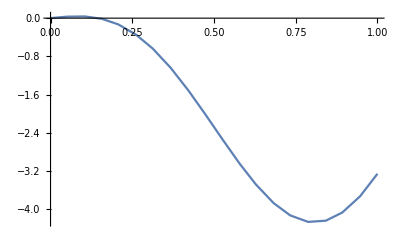

```mathematica
Plot[c2β[τ], {τ, 0, 1}, PlotPoints->20, MaxRecursion->0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.98979×10^-8 and 1.33933×10^-8 for the integral and error estimates.

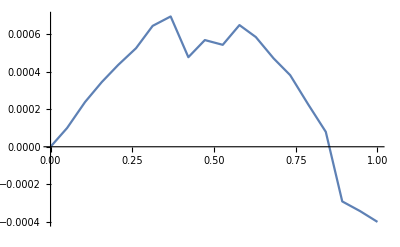

```mathematica
Plot[cβ[τ], {τ, 0, 1}, PlotPoints->20, MaxRecursion->0]
```

```mathematica
EffG[g1, gFrame, 0, 0] - EffG[g2, {0, 0, 0}, 0, 0]
ArcTan[1/(1 - 1)]
```

-0.427728

Power::infy: Infinite expression 1/0 encountered.

Indeterminate

```mathematica
Minimize[xi[dipolar, JJ, B0, θ, ϕ], {θ, ϕ}]
```

{-3.14159,{θ→0.94288,ϕ→0.370308}}

```mathematica
g2
```

{2.01,2.01,2.01}

```mathematica
cβ0[θ_, ϕ_, τ_] := Sin[2*(JJ - dd[dipolar, θ])*τ]*Sin[2xi[dipolar, JJ, B0, θ, ϕ]]^2;
cβ[τ_] := NIntegrate[Sin[θ]*cβ0[θ, ϕ, 0.0000001], {θ, 0, Pi}, {ϕ, 0, 2Pi}];
Plot[cβ[τ], {τ, 0, 10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.78134×10^-11-2.53407×10^-12 ⅈ and 9.9566×10^-17 for the integral and error estimates.

NIntegrate::inumr: The integrand (Sin[θ] (0.000056-0.0047642 (-1/3+Cos[θ]^2)+0.0324902/(√Plus[«3»]-1. Power[«2»]))^2 Sin[2 τ (0.000028+0.0047642 (-1/3+Cos[«1»]^2))])/(1+(0.000056-0.0047642 (-1/3+Power[«2»])+0.0324902/Plus[«2»])^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.14159},{0,6.28319}}.

```mathematica
NIntegrate[Sin[2*(JJ - dipolar*(Cos[θ]^2 - 1/3))*τ], {θ, 0, Pi}, {ϕ, 0, 2Pi}]
```

NIntegrate::inumr: The integrand Sin[2 τ (0.000028+0.0047642 (-1/3+Cos[θ]^2))] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.14159},{0,6.28319}}.

NIntegrate[Sin[2 (JJ-dipolar (Cos[θ]^2-1/3)) τ],{θ,0,π},{ϕ,0,2 π}]

```mathematica
Dot[#^2 & /@ {a, b, c}, #^2 & /@{x, y, z}]
```

a^2 x^2+b^2 y^2+c^2 z^2

```mathematica
N[(Sqrt[Dot[#^2 & /@ rVers[θ, ϕ], #^2 & /@ erot[gFrame].g1.Transpose[erot[gFrame]]]] - Sqrt[Dot[#^2 & /@ rVers[θ, ϕ], #^2 & /@ g2]])]
```

√(0.52502 Cos[θ]^2-3.20582 Cos[ϕ]^2 Sin[θ]^2-1.20294 Sin[θ]^2 Sin[ϕ]^2)-1. √(4.0401 Cos[θ]^2+4.0401 Cos[ϕ]^2 Sin[θ]^2+4.0401 Sin[θ]^2 Sin[ϕ]^2)